```mathematica
a=(1/2+I*1/2)*0.9925
```

0.49625+0.49625 ⅈ

```mathematica
c=(-1/2+I*1/2)*0.9925
```

-0.49625+0.49625 ⅈ

```mathematica
d=(1/2+I*1/2)*0.1219
```

0.06095+0.06095 ⅈ

```mathematica
b=(-1/2+I*1/2)*0.1219
```

-0.06095+0.06095 ⅈ

```mathematica
top=a+b
```

0.4353+0.5572 ⅈ

```mathematica
bottom=c+d
```

-0.4353+0.5572 ⅈ

```mathematica
A=top*2/I
```

1.1144-0.8706 ⅈ

```mathematica
B=bottom*2/I
```

1.1144+0.8706 ⅈ

```mathematica
1.187*180/Pi
```

68.0101

```mathematica
3.057*180/Pi
```

175.153

```mathematica
Pi/8*180/Pi
```

45/2

```mathematica
(-Sqrt[1.5^2-2])/1.5*90
```

-30.

## Lab 6.9

```mathematica
alpha=12*Pi/180;
theta=70*Pi/180;
```

```mathematica
L={{Cos[alpha]},{Sin[alpha]}}
L//MatrixForm
```

{{Cos[π/15]},{Sin[π/15]}}

(Cos[π/15]
Sin[π/15])

```mathematica
M = {{Cos[theta]^2+I*Sin[theta]^2,(1-I)*Sin[theta]*Cos[theta]},{(1-I)*Sin[theta]*Cos[theta],Sin[theta]^2+I*Cos[theta]^2}}
```

{{ⅈ Cos[π/9]^2+Sin[π/9]^2,(1-ⅈ) Cos[π/9] Sin[π/9]},{(1-ⅈ) Cos[π/9] Sin[π/9],Cos[π/9]^2+ⅈ Sin[π/9]^2}}

```mathematica
M//MatrixForm
```

(ⅈ Cos[π/9]^2+Sin[π/9]^2 | (1-ⅈ) Cos[π/9] Sin[π/9]
(1-ⅈ) Cos[π/9] Sin[π/9] | Cos[π/9]^2+ⅈ Sin[π/9]^2)

```mathematica
Simplify[Inverse[M].L]
```

{{(1/2-ⅈ/2) (Cos[π/15]-ⅈ Sin[(19 π)/90])},{(1/2+ⅈ/2) (Cos[(19 π)/90]-ⅈ Sin[π/15])}}

```mathematica
%//MatrixForm
```

((1/2-ⅈ/2) (Cos[π/15]-ⅈ Sin[(19 π)/90])
(1/2+ⅈ/2) (Cos[(19 π)/90]-ⅈ Sin[π/15]))

```mathematica
Pi/15*180/Pi
```

12

```mathematica
19*Pi/90*180/Pi
```

38

```mathematica
N[Expand[(1/2-I/2)*(Cos[Pi/15]-I*Sin[(19*Pi)/90])]]
```

0.181243-0.796905 ⅈ

```mathematica
N[Expand[(1/2+I/2)*(Cos[19*Pi/90]-I*Sin[Pi/15])]]
```

0.497961+0.29005 ⅈ

```mathematica
zB=Sqrt[0.497961^2+0.29005^2]
```

0.576276

```mathematica
deltaB=ArcTan[0.29005/0.497961]*180/Pi
```

30.2197

```mathematica
zA=Sqrt[0.181243^2+0.796905^2]
```

0.817256

```mathematica
deltaA=ArcTan[0.796905/0.181243]*180/Pi
```

77.187

```mathematica
A=0.817256;
B=0.576276;
Delta=30.2197*Pi/180;
Alpha=12*Pi/180;
```

```mathematica
Emax=Sqrt[A^2*Cos[Alpha]^2+B^2*Sin[Alpha]^2+A*B*Cos[Delta]*Sin[2*Alpha]]
Emin=Sqrt[A^2*Sin[Alpha]^2+B^2*Cos[Alpha]^2-A*B*Cos[Delta]*Sin[2*Alpha]]
```

0.904941

0.42554

```mathematica
Emin/Emax
```

0.470241

## Problem 6.14

```mathematica
n=1.5;
```

```mathematica
deltas=2*ArcTan[Sqrt[n^2*Sin[thetai]^2-1]/(n*Cos[thetai])];
```

```mathematica
deltap=2*ArcTan[(n*Sqrt[n^2*Sin[thetai]^2-1])/Cos[thetai]];
```

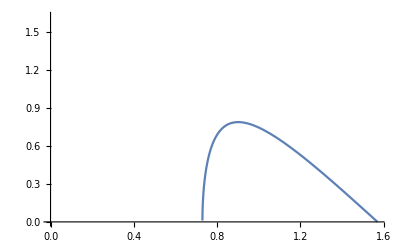

```mathematica
Plot[deltap-deltas,{thetai,0,Pi/2}]
```

```mathematica
FindMinimum[deltap-deltas,{thetai,1}]
```

FindMinimum::nrnum: The function value -3.14159-0.195242 ⅈ is not a real number at {thetai} = {2.897}.

{0.74682,{thetai→1.}}

```mathematica
0.74682*180/Pi
```

42.7896

```mathematica
(*I am close to 50, but I am off by 8 degrees.*)
```